```mathematica
$DefaultThickness=.004;
Unprotect[Plot];
Plot[heads___,PlotStyle->Automatic,tails___]:=Plot[heads,PlotStyle->Thickness[$DefaultThickness],tails];
Plot[heads___,PlotStyle->style_/;!ListQ[style]&&FreeQ[style,Thickness],tails___]:=Plot[heads,PlotStyle->{{style,Thickness[$DefaultThickness]}},tails];
Plot[heads___,PlotStyle->{h___,style_,t___}/;FreeQ[style,Thickness],tails___]:=Plot[heads,PlotStyle->{h,Flatten[{style,Thickness[$DefaultThickness]}],t},tails];
Plot[args_/;FreeQ[{args},PlotStyle]]:=Plot[args,Evaluate[PlotStyle->(PlotStyle/.Options[Plot])]];
Protect[Plot];
```

1. Add a default PointSize to the ListPlot function.

```mathematica
$PointSize=.1;
```

```mathematica
Unprotect[ListPlot];
ListPlot[heads___,PlotStyle->Automatic,tails___]:=ListPlot[heads,PlotStyle->{PointSize[$PointSize]},tails];
ListPlot[heads___,PlotStyle->style_/;!ListQ[style]&&FreeQ[style,PointSize],tails___]:=ListPlot[heads,PlotStyle->{style,PointSize[$PointSize]},tails];
ListPlot[heads___,PlotStyle->{h___,style_/;FreeQ[style,PointSize],t___},tails___]:=ListPlot[heads,PlotStyle->{h,Flatten[{style,PointSize[$PointSize]}],t},tails];
ListPlot[args_/;FreeQ[args,PointSize]]:=ListPlot[args,PlotStyle->{PlotStyle/.Options[Plot]}];
Protect[ListPlot];
```

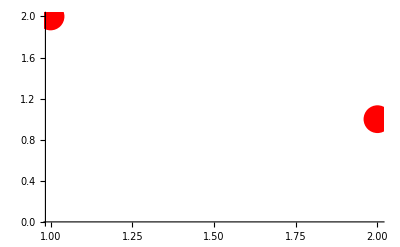

```mathematica
$PointSize=0.05;
ListPlot[{{1,2},{2,1}},PlotStyle->Red]
```

```mathematica
Unprotect[ListPlot];DownValues[ListPlot]=RotateLeft[DownValues[ListPlot]];Protect[Plot];
```

```mathematica
First/@DownValues[ListPlot]
```

{HoldPattern[ListPlot[heads___,PlotStyle→Automatic,tails___]],HoldPattern[ListPlot[heads___,PlotStyle→style_/;!ListQ[style]&&FreeQ[style,PointSize],tails___]],HoldPattern[ListPlot[heads___,PlotStyle→{h___,style_/;FreeQ[style,PointSize],t___},tails___]],HoldPattern[ListPlot[args_/;FreeQ[args,PointSize]]],HoldPattern[(ListPlot[System`ProtoPlotDump`a__,System`ProtoPlotDump`o:OptionsPattern[]])?(Function[System`ProtoPlotDump`arg,Charting`ChartArgCheck[System`ProtoPlotDump`arg,System`ProtoPlotDump`iListPlot,1],HoldFirst])]}

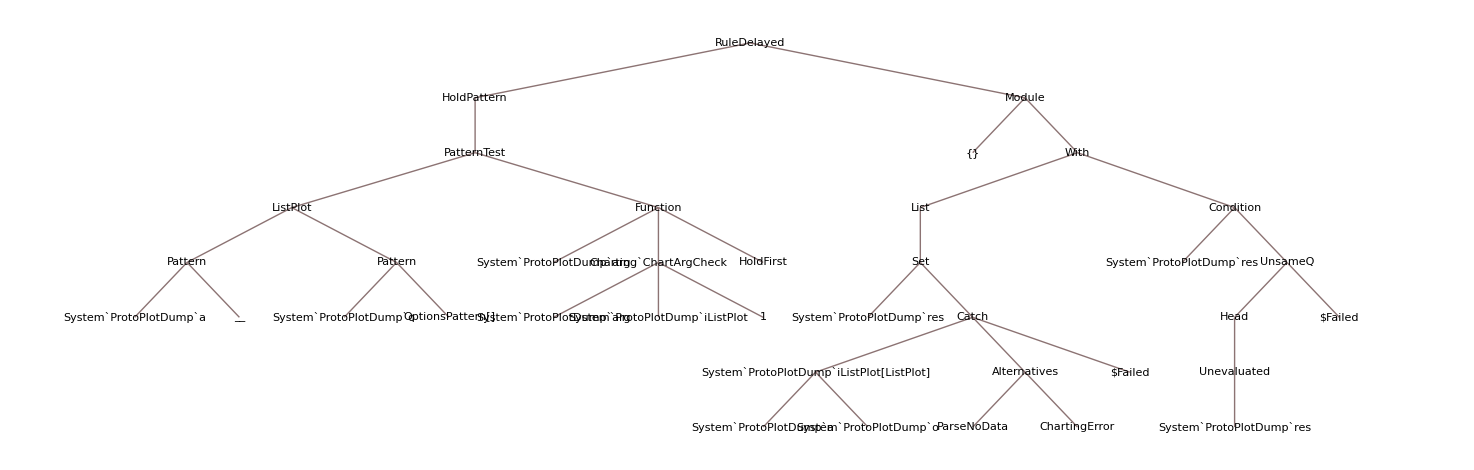

```mathematica
DownValues[ListPlot][[1]]//TreeForm
```

```mathematica
DownValues[Plot]
```

{HoldPattern[Plot[heads___,PlotStyle→Automatic,tails___]]:>Plot[heads,PlotStyle→Thickness[$DefaultThickness],tails],HoldPattern[Plot[heads___,PlotStyle→style_/;!ListQ[style]&&FreeQ[style,Thickness],tails___]]:>Plot[heads,PlotStyle→{{style,Thickness[$DefaultThickness]}},tails],HoldPattern[Plot[heads___,PlotStyle→{h___,style_,t___}/;FreeQ[style,Thickness],tails___]]:>Plot[heads,PlotStyle→{h,Flatten[{style,Thickness[$DefaultThickness]}],t},tails],HoldPattern[Plot[args_/;FreeQ[{args},PlotStyle]]]:>Plot[args,Evaluate[PlotStyle→(PlotStyle/.Options[Plot])]],HoldPattern[(Plot[System`ProtoPlotDump`a:PatternSequence[___,Except[_?System`Dump`HeldOptionQ]]|PatternSequence[],System`ProtoPlotDump`o:OptionsPattern[]])?(Function[System`ProtoPlotDump`arg,Charting`PlotArgCheck[System`ProtoPlotDump`arg,System`ProtoPlotDump`iPlot,2],HoldFirst])]:>Module[{},With[{System`ProtoPlotDump`res=Catch[System`ProtoPlotDump`iPlot[System`ProtoPlotDump`a,System`ProtoPlotDump`o],ParseNoData|ChartingError,$Failed]},System`ProtoPlotDump`res/;Head[Unevaluated[System`ProtoPlotDump`res]]=!=$Failed]]}